## Initial Value

```mathematica
Clear["Global`*"]
```

```mathematica
Plot[h[t_*10^-12],{t,0,800},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1}]
```

-Graphics-

```mathematica
-Graphics-
Fc= 200*10^12 ;(*搬送波の周波数[Hz]*)
Print[Fc, "Hz"]
```

-Graphics-

200000000000000Hz

```mathematica
c[i]= Sin[2*Pi*Fc*i]
```

Sin[400000000000000 i π]

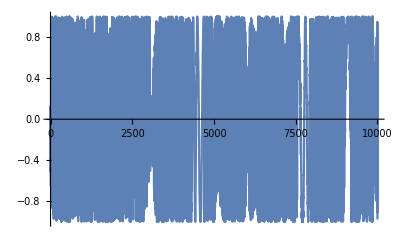

```mathematica
Plot[c[i], {i,0,10000 }]
```

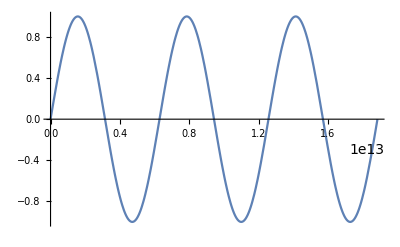

```mathematica
Plot[Sin[x*10^-12],{x,0,6*10^12 Pi}]
```

```mathematica
Plot[c[i*10^-12],{i,0,100 },PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},
BaseStyle->{Bold,FontSize->15},PlotRange->{-1,1}]
```

-Graphics-

Cos[399980000000000 i π]+Cos[400020000000000 i π]+Sin[400000000000000 i π]

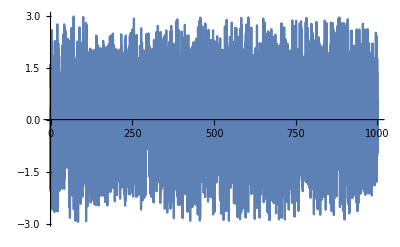

```mathematica
AM[i]=c[i]+ Cos[2Pi(Fc+10*10^9)i]+Cos[2Pi(Fc-10*10^9)i]
Plot[AM[i],{i,0,1000},PlotPoints->100]
```

```mathematica
AM[i]=c[i]+ Cos[2Pi(Fc+10*10^9)i]+Cos[2Pi(Fc-10*10^9)i]
Plot[AM[i],{i,0,1000},PlotPoints->100]
```

Cos[399980000000000 i π]+Cos[400020000000000 i π]+Sin[400000000000000 i π]

-Graphics-

## Initial Value

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

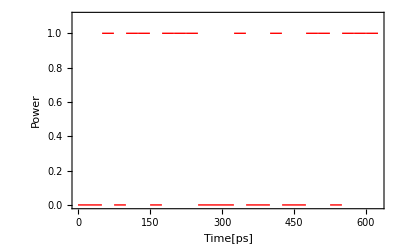

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,25}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

```mathematica
bit=25;
For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]
```

{0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1}

```mathematica
f[x]=5x
Plot[f[x*10],{x,0,1000}]
```

5 x

-Graphics-

Cos[400000000000000 π t]

Sin[t]

0

1

0

1

Cos[400000000000000 π t] Sin[t]

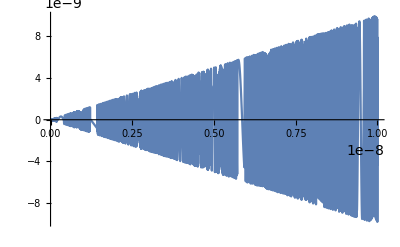

```mathematica
Fc= 200*10^12 ;(*搬送波の周波数[Hz]*)
carrier[t]= Cos[2*Pi*Fc*t]
signal[t]=Sin[t]
signal1[0]=0
signal1[1]=1
signal1[2]=0
signal1[3]=1
cs2[t]=carrier[t]*signal[t]
Plot[cs2[t],{t,0,10000*10^-12}]
```

Set::write: h xのタグTimesはProtectedです．

ⅇ^(ⅈ x)

2.03931×10^-23

ⅇ^((0.+8.15722×10^-22 ⅈ) (-1.2161×10^15+w)^2)

{Cos[x]}

Set::write: Re[H_cmp[w]]のタグReはProtectedです．

1. Cos[0.+8.15722×10^-22 (-1.2161×10^15+w)^2]

Rule::rhs: パターンH_cmpは規則System`ComplexExpandDump`reimexpr[H_cmp[w]]→{H_cmp[w],0}の右辺にあります．

Rule::rhs: パターンH_cmpは規則System`ComplexExpandDump`reimexpr[Re[H_cmp[w]]]→{H_cmp[w],0}の右辺にあります．

H_cmp[w]

-Graphics-

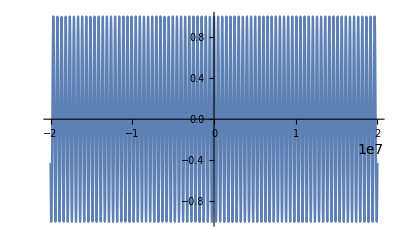

```mathematica
L=80;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
w2=2*Pi*c/λ;
h(x)=Exp[I*x]
β2
H_cmp[w]=Exp[1/2*β2*I*L(w-w2)^2]
ComplexExpand[Re[E^{I*x}]]
Re[H_cmp[w]]=ComplexExpand[Re[Exp[1/2*β2*I*L(w-w2)^2]]]
ComplexExpand[Re[H_cmp[w]]]
(*Re[H_cmp[w]]:=Cos [1/2 * β2*L(w-w2)^2]*)
Plot[Exp[w],{w,0,200}]
Plot[ComplexExpand[Re[Exp[1/2*β2*I*L(2*Pi*f-w2)^2]]],{f,-200*10^5,200*10^5}]
```

-Graphics-

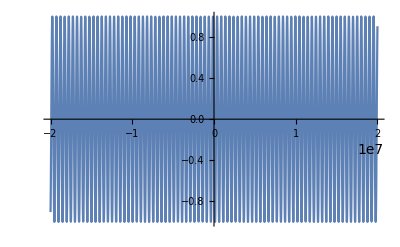

```mathematica
Plot[1/((2 Pi β2 L)^1/2)*Cos [1/2 * β2*L*(2*Pi*f-w2)^2],{f,-200*10^4,200*10^4}]
Plot[ComplexExpand[Im[Exp[1/2*β2*I*L(2*Pi*f-w2)^2]]],{f,-200*10^5,200*10^5}]
```

```mathematica
(*時間軸応答*)
h_cmp[t]=1/(2*Pi*β2*L)*Exp[-I*((t^2)/2*β2*L-Pi/4)]
ComplexExpand[Re[1/(2*Pi*β2*L)*Exp[-I*((t^2)/(2*β2*L)-Pi/4)]]]
Plot[ComplexExpand[Re[1/(2*Pi*β2*L)*Exp[-I*((t^2)/(2*β2*L)-Pi/4)]]],{t,-100*10^-11,100*10^-11}]
Plot[9.755463059313215*^19 Cos[0.7853981633974483-3.0647691079505006*^20 t^2],{t,-100*10^-11,100*10^-11}]
```

9.75546×10^19 ⅇ^(-ⅈ (-π/4+8.15722×10^-22 t^2))

(0.+0. ⅈ)+9.75546×10^19 Cos[0.785398-3.06477×10^20 t^2]

-Graphics-

-Graphics-

```mathematica
Plot[ComplexExpand[Im[1/(2*Pi*β2*L)*Exp[-I*((t^2)/(2*β2*L)-Pi/4)]]],{t,-100*10^-11,100*10^-11}]
(*逆フーリエ変換*)
(*∫_-Infinity^Infinity Exp[1/2*β2*I*L(2*Pi*f-w2)^2]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1*)
InverseFourierTransform[Exp[1/2*β2*I*L(w-w2)^2],ω,t]
ComplexExpand[Re[InverseFourierTransform[Exp[1/2*β2*I*L(w-w2)^2],ω,t]]]
(*Plot[ComplexExpand[Im[InverseFourierTransform[Exp[1/2*β2*I*L(w-w2)^2],ω,t]]],{t,-200*10^-11,200*10^-11}]*)
```

-Graphics-

ⅇ^((0.+8.15722×10^-22 ⅈ) (-1.2161×10^15+w)^2) √(2 π) DiracDelta[t]

2.50663 Cos[0.+8.15722×10^-22 (-1.2161×10^15+w)^2] DiracDelta[t]

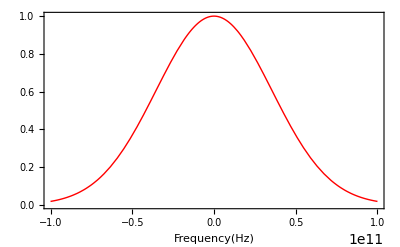

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
}
```

```mathematica
{Cos[x]}
```

{Cos[x]}

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

-Graphics-

```mathematica
mado[f]*Exp[1/2*β2*I*L(2*Pi*f-w2)^2]
```

ⅇ^(-3.98107×10^-22 f^2+(0.+8.15722×10^-22 ⅈ) (-1.2161×10^15+2 f π)^2)

```mathematica
ⅇ^(-3.9810717055349856*^-22 f^2+(0.+8.157221349936609*^-22 ⅈ) (-1.2161003820347585*^15+2 f π)^2)
```

ⅇ^(-3.98107×10^-22 f^2+(0.+8.15722×10^-22 ⅈ) (-1.2161×10^15+2 f π)^2)

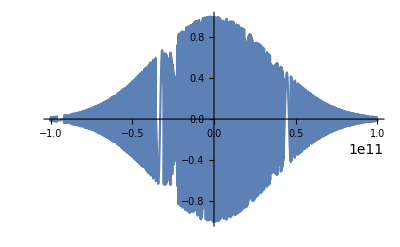

```mathematica
Plot[mado[f]*ComplexExpand[Re[Exp[1/2*β2*I*L(2*Pi*f-w2)^2]]],{f,-100*10^9,100*10^9}]
```

```mathematica
(*Plot[ⅇ^(-3.9810717055349856*^-22 f^2+(0.+8.157221349936609*^-22 ⅈ) (-1.2161003820347585*^15+2 f π)^2),{f,-100*10^5,100*10^5}]*)
```

100

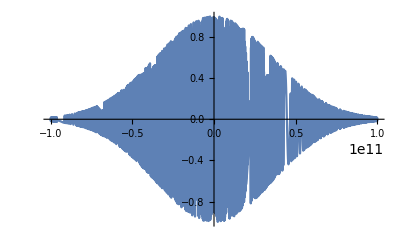

```mathematica
L=100
Plot[mado[f]*ComplexExpand[Re[Exp[1/2*β2*I*L(2*Pi*f-w2)^2]]],{f,-100*10^9,100*10^9}]
```

```mathematica
FourierTransform[Sin[400*Pi*t],t,ω]
```

ⅈ √(π/2) DiracDelta[-400 π+ω]-ⅈ √(π/2) DiracDelta[400 π+ω]

ⅈ √(π/2) DiracDelta[-400 π+ω]-ⅈ √(π/2) DiracDelta[400 π+ω]

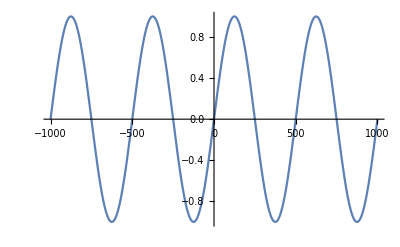

```mathematica
ⅈ √(π/2) DiracDelta[-400 π+ω]-ⅈ √(π/2) DiracDelta[400 π+ω]
Plot[Sin[400*Pi*t*10^-5],{t,-1000,1000}]
```

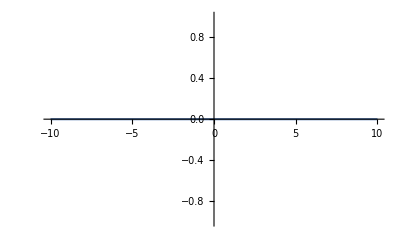

```mathematica
Fs[ω]:=ⅈ √(π/2) DiracDelta[-400 π+ω]-ⅈ √(π/2) DiracDelta[400 π+ω]
Plot[(Re[Fs[ω]]^2+Im[Fs[ω]]^2),{ω,-10,10}]
```

```mathematica
Fc=200;(*搬送波周波数[THz]*)
```

```mathematica
H_dis[ω]=Exp[-1/2*I(ω-2*Pi*Fc)^2*β2*L]
```

ⅇ^((0.-1.01965×10^-21 ⅈ) (-400 π+ω)^2)

```mathematica
ⅇ^(-1/2 ⅈ L β2 (ω-ω0)^2)
```

ⅇ^((0.-1.01965×10^-21 ⅈ) (ω-ω0)^2)

```mathematica
H_dis[ω]
```

H_dis[ω]

```mathematica
InverseFourierTransform[H_dis[ω],ω,t]
```

InverseFourierTransform[H_dis[ω],ω,t]

```mathematica
InverseFourierTransform[H_dis[ω],ω,t]
InverseFourierTransform[Exp[-1/2*β2*L*I(ω-2*Pi*Fc)^2],ω,t]
InverseFourierTransform[Exp[-1/2*β2*L*I*{ω-2*Pi*Fc}^2],ω,t]
```

InverseFourierTransform[H_dis[ω],ω,t]

(1.56583×10^10-1.56583×10^10 ⅈ) ⅇ^((0.+2.45182×10^20 ⅈ) (-2.56267×10^-18+t)^2)

{(1.56583×10^10-1.56583×10^10 ⅈ) ⅇ^((0.+2.45182×10^20 ⅈ) (-2.56267×10^-18+t)^2)}

{(5.73133×10^9+2.13896×10^10 ⅈ) ⅇ^((0.+2.45182×10^20 ⅈ) (-2.56267×10^-6+t)^2)}

```mathematica
FourierTransform[Exp[-1/2*β2*L*I*{ω-2*Pi*Fc}^2],ω,t,FourierParameters->{1,-1}]
```

{(3.92495×10^10-3.92495×10^10 ⅈ) ⅇ^((0.+2.45182×10^20 ⅈ) (-2.56267×10^-18+t)^2)}

```mathematica
Re[(5.731325718865109*^9+2.1389599406635815*^10 ⅈ) ⅇ^((0.+2.4518152863604002*^20 ⅈ) (2.562666666666667*^-6+t)^2)]
```

Re[(5.73133×10^9+2.13896×10^10 ⅈ) ⅇ^((0.+2.45182×10^20 ⅈ) (2.56267×10^-6+t)^2)]

```mathematica
Plot[[Re[(5.731325718865109*^9+2.1389599406635815*^10 ⅈ) ⅇ^((0.+2.4518152863604002*^20 ⅈ) (2.562666666666667*^-6+t)^2)]],{t,-100,100}]
```

```mathematica
ComplexExpand[Re[(5.731325718865109*^9+2.1389599406635815*^10 ⅈ) ⅇ^((0.+2.4518152863604002*^20 ⅈ) (2.562666666666667*^-6+t)^2)]]
```

5.73133×10^9 Cos[0.+2.45182×10^20 (2.56267×10^-6+t)^2]-2.13896×10^10 Sin[0.+2.45182×10^20 (2.56267×10^-6+t)^2]

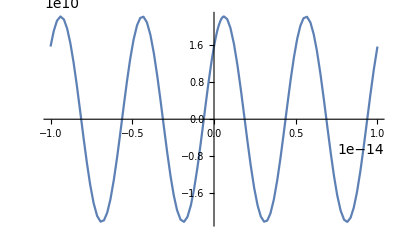

```mathematica
Plot[5.731325718865109*^9 Cos[0.+2.4518152863604002*^20 (2.562666666666667*^-6+t)^2]-2.1389599406635815*^10 Sin[0.+2.4518152863604002*^20 (2.562666666666667*^-6+t)^2],{t,-1*10^-14,10^-14}]
```

```mathematica
Factor[I((ω Cos[50 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[75 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[100 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[150 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[175 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[250 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[325 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[350 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[400 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[425 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[475 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[525 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[550 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[650 ω])/(√(2 π) (-160000 π^2+ω^2)))-(ω Sin[50 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[75 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[100 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[150 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[175 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[250 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[325 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[350 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[400 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[425 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[475 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[525 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[550 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[650 ω])/(√(2 π) (-160000 π^2+ω^2))]
```

(ω (-ⅈ Cos[50 ω]+ⅈ Cos[75 ω]-ⅈ Cos[100 ω]+ⅈ Cos[150 ω]-ⅈ Cos[175 ω]+ⅈ Cos[250 ω]-ⅈ Cos[325 ω]+ⅈ Cos[350 ω]-ⅈ Cos[400 ω]+ⅈ Cos[425 ω]-ⅈ Cos[475 ω]+ⅈ Cos[525 ω]-ⅈ Cos[550 ω]+ⅈ Cos[650 ω]+Sin[50 ω]-Sin[75 ω]+Sin[100 ω]-Sin[150 ω]+Sin[175 ω]-Sin[250 ω]+Sin[325 ω]-Sin[350 ω]+Sin[400 ω]-Sin[425 ω]+Sin[475 ω]-Sin[525 ω]+Sin[550 ω]-Sin[650 ω]))/(√(2 π) (400 π-ω) (400 π+ω))

```mathematica
InverseFourierTransform[(Cos[(-1.01965*10^-21 )*(-400 π+ω*10^12)^2]+I Sin[(-1.019652*10^-21 ) (-400 π+ω*10^12)^2])*((ω (I (-Cos[50 ω]+Cos[75 ω]-Cos[100 ω]+Cos[150 ω]-Cos[175 ω]+Cos[250 ω]-Cos[325 ω]+Cos[350 ω]-Cos[400 ω]+Cos[425 ω]-Cos[475 ω]+Cos[525 ω]-Cos[550 ω]+Cos[650 ω])+Sin[50 ω]-Sin[75 ω]+Sin[100 ω]-Sin[150 ω]+Sin[175 ω]-Sin[250 ω]+Sin[325 ω]-Sin[350 ω]+Sin[400 ω]-Sin[425 ω]+Sin[475 ω]-Sin[525 ω]+Sin[550 ω]-Sin[650 ω]))/(√(2 π) (400 π-ω) (400 π+ω))),ω,t]
```

$Aborted

```mathematica
Hdis[ω_]=Exp[-1/2*I[ω-2*Pi*Fc]^2*β2*L]
Plot[Re[ⅇ^(-1.0196526687420762*^-21 ⅈ[-400 π+ω]^2)],{ω,-1*10^11,1*10^11}]
```

ⅇ^(-1.01965×10^-21 ⅈ[-400 π+ω]^2)

-Graphics-

```mathematica
ⅇ^(0.-1.0196526687420762*^-21 ⅈ)
```

1.-1.01965×10^-21 ⅈ

```mathematica
InverseFourierTransform[(-0.3989 ω Cos[1.610*^-15-2.563*^-6 ω+1019.65 ω^2] Sin[50 ω]+I(0.3989ω Cos[50 ω] Cos[1.610*^-15-2.563*^-6 ω+1019.65 ω^2])(*0.3989422804014327 ω Cos[1.6101667404113218*^-15-2.562659959386266*^-6 ω+1019.6499999999999 ω^2] Sin[75 ω]-0.3989422804014327 ω Cos[1.6101667404113218*^-15-2.562659959386266*^-6 ω+1019.6499999999999 ω^2] Sin[100 ω]+0.3989422804014327 ω Cos[1.6101667404113218*^-15-2.562659959386266*^-6 ω+1019.6499999999999 ω^2] Sin[150 ω]-0.3989422804014327 ω Cos[1.6101667404113218*^-15-2.562659959386266*^-6 ω+1019.6499999999999 ω^2] Sin[175 ω]*))*1/(-160000 π^2+ω^2),ω,t]
```

$Aborted